We attempt to solve the full dispersion relation

```mathematica
hminus = ReplaceAll[1/2((c^2 (γ̄)^8+c^4 K^2 V^4 (γ̄)^2 Subscript[k, x]^4+(c^2+2 V^2) (γ̄)^6 (c^2 Subscript[k, x]^2+(c^2+V^2) Subscript[k, y]^2)+c^2 V^2 (γ̄)^4 Subscript[k, x]^2 ((2 c^2+V^2) Subscript[k, x]^2+(2 c^2+3 V^2) Subscript[k, y]^2))/(L ((γ̄)^2+V^2 Subscript[k, x]^2) ((c^2+V^2) (γ̄)^2+c^2 V^2 Subscript[k, x]^2) (K^2 (c^2+V^2) (γ̄)^2+(γ̄)^4+c^2 K^2 V^2 Subscript[k, x]^2))-√(((c^2 (γ̄)^8+c^4 K^2 V^4 (γ̄)^2 Subscript[k, x]^4+(c^2+2 V^2) (γ̄)^6 (c^2 Subscript[k, x]^2+(c^2+V^2) Subscript[k, y]^2)+c^2 V^2 (γ̄)^4 Subscript[k, x]^2 ((2 c^2+V^2) Subscript[k, x]^2+(2 c^2+3 V^2) Subscript[k, y]^2))^2+4 ((γ̄)^2+V^2 Subscript[k, x]^2) ((c^2+V^2) (γ̄)^2+c^2 V^2 Subscript[k, x]^2) (K^2 (c^2+V^2) (γ̄)^2+(γ̄)^4+c^2 K^2 V^2 Subscript[k, x]^2) (L^2 (γ̄)^10+c^4 K^4 L^2 V^6 Subscript[k, x]^6+L^2 (γ̄)^8 ((2 c^2+3 V^2) Subscript[k, x]^2+2 (c^2+V^2) Subscript[k, y]^2)+K^2 L^2 (γ̄)^6 ((c^4+6 c^2 V^2+3 V^4) Subscript[k, x]^2+(c^2+V^2)^2 Subscript[k, y]^2)+K^2 V^2 (γ̄)^4 (L^2 (3 c^4+6 c^2 V^2+V^4) Subscript[k, x]^4+(c^2+V^2) (2 c^2+L^2 (3 c^2+V^2) Subscript[k, x]^2) Subscript[k, y]^2)+c^2 K^2 V^4 (γ̄)^2 Subscript[k, x]^2 (L^2 (3 c^2+2 V^2) Subscript[k, x]^4+(2 c^2+L^2 (3 c^2+2 V^2) Subscript[k, x]^2) Subscript[k, y]^2)))/(L^2 ((γ̄)^2+V^2 Subscript[k, x]^2)^2 ((c^2+V^2) (γ̄)^2+c^2 V^2 Subscript[k, x]^2)^2 (K^2 (c^2+V^2) (γ̄)^2+(γ̄)^4+c^2 K^2 V^2 Subscript[k, x]^2)^2))),{c->√(P/ρ1),V->B/(√(μ*ρ1)),γ̄->(γ+I*kx*U1),L->(P/ρ1)/g,Subscript[k, x]->kx,Subscript[k, y]->ky,K->√(kx^2+ky^2)}];
```

```mathematica
hplus = ReplaceAll[1/2((c^2 (γ̄)^8+c^4 K^2 V^4 (γ̄)^2 Subscript[k, x]^4+(c^2+2 V^2) (γ̄)^6 (c^2 Subscript[k, x]^2+(c^2+V^2) Subscript[k, y]^2)+c^2 V^2 (γ̄)^4 Subscript[k, x]^2 ((2 c^2+V^2) Subscript[k, x]^2+(2 c^2+3 V^2) Subscript[k, y]^2))/(L ((γ̄)^2+V^2 Subscript[k, x]^2) ((c^2+V^2) (γ̄)^2+c^2 V^2 Subscript[k, x]^2) (K^2 (c^2+V^2) (γ̄)^2+(γ̄)^4+c^2 K^2 V^2 Subscript[k, x]^2))+√(((c^2 (γ̄)^8+c^4 K^2 V^4 (γ̄)^2 Subscript[k, x]^4+(c^2+2 V^2) (γ̄)^6 (c^2 Subscript[k, x]^2+(c^2+V^2) Subscript[k, y]^2)+c^2 V^2 (γ̄)^4 Subscript[k, x]^2 ((2 c^2+V^2) Subscript[k, x]^2+(2 c^2+3 V^2) Subscript[k, y]^2))^2+4 ((γ̄)^2+V^2 Subscript[k, x]^2) ((c^2+V^2) (γ̄)^2+c^2 V^2 Subscript[k, x]^2) (K^2 (c^2+V^2) (γ̄)^2+(γ̄)^4+c^2 K^2 V^2 Subscript[k, x]^2) (L^2 (γ̄)^10+c^4 K^4 L^2 V^6 Subscript[k, x]^6+L^2 (γ̄)^8 ((2 c^2+3 V^2) Subscript[k, x]^2+2 (c^2+V^2) Subscript[k, y]^2)+K^2 L^2 (γ̄)^6 ((c^4+6 c^2 V^2+3 V^4) Subscript[k, x]^2+(c^2+V^2)^2 Subscript[k, y]^2)+K^2 V^2 (γ̄)^4 (L^2 (3 c^4+6 c^2 V^2+V^4) Subscript[k, x]^4+(c^2+V^2) (2 c^2+L^2 (3 c^2+V^2) Subscript[k, x]^2) Subscript[k, y]^2)+c^2 K^2 V^4 (γ̄)^2 Subscript[k, x]^2 (L^2 (3 c^2+2 V^2) Subscript[k, x]^4+(2 c^2+L^2 (3 c^2+2 V^2) Subscript[k, x]^2) Subscript[k, y]^2)))/(L^2 ((γ̄)^2+V^2 Subscript[k, x]^2)^2 ((c^2+V^2) (γ̄)^2+c^2 V^2 Subscript[k, x]^2)^2 (K^2 (c^2+V^2) (γ̄)^2+(γ̄)^4+c^2 K^2 V^2 Subscript[k, x]^2)^2))),{c->√(P/ρ2),V->B/(√(μ*ρ2)),γ̄->(γ+I*kx*U2),L->(P/ρ2)/g,Subscript[k, x]->kx,Subscript[k, y]->ky,K->√(kx^2+ky^2)}];
```

```mathematica
disp=ReplaceAll[-(hminus (B^2 Subscript[c, 1]^2 Subscript[k, x]^2+(B^2+P μ) Subscript[γ̄, 1]^2) (Subscript[k, x]^2 Subscript[k, y]^2 Subscript[V, 1]^4+K^2 Subscript[V, 1]^2 Subscript[γ̄, 1]^2+Subscript[γ̄, 1]^4))/(μ (Subscript[γ̄, 1]^2 (K^2 Subscript[V, 1]^2+Subscript[γ̄, 1]^2) (Subscript[k, y]^2 Subscript[V, 1]^2+Subscript[γ̄, 1]^2)+K^2 Subscript[c, 1]^2 (Subscript[k, x]^2 Subscript[k, y]^2 Subscript[V, 1]^4+K^2 Subscript[V, 1]^2 Subscript[γ̄, 1]^2+Subscript[γ̄, 1]^4)))+(hplus (B^2 Subscript[c, 2]^2 Subscript[k, x]^2+(B^2+P μ) Subscript[γ̄, 2]^2) (Subscript[k, x]^2 Subscript[k, y]^2 Subscript[V, 2]^4+K^2 Subscript[V, 2]^2 Subscript[γ̄, 2]^2+Subscript[γ̄, 2]^4))/(μ (Subscript[γ̄, 2]^2 (K^2 Subscript[V, 2]^2+Subscript[γ̄, 2]^2) (Subscript[k, y]^2 Subscript[V, 2]^2+Subscript[γ̄, 2]^2)+K^2 Subscript[c, 2]^2 (Subscript[k, x]^2 Subscript[k, y]^2 Subscript[V, 2]^4+K^2 Subscript[V, 2]^2 Subscript[γ̄, 2]^2+Subscript[γ̄, 2]^4)))+g (-ρ1+ρ2+(Subscript[γ̄, 1]^2 (P μ (K^2 Subscript[V, 1]^2+Subscript[γ̄, 1]^2) (Subscript[k, y]^2 Subscript[V, 1]^2+Subscript[γ̄, 1]^2)+B^2 Subscript[c, 1]^2 ((-K^4+Subscript[k, x]^2 (K^2+Subscript[k, y]^2)) Subscript[V, 1]^2+Subscript[k, y]^2 Subscript[γ̄, 1]^2)))/(μ Subscript[c, 1]^2 (Subscript[γ̄, 1]^2 (K^2 Subscript[V, 1]^2+Subscript[γ̄, 1]^2) (Subscript[k, y]^2 Subscript[V, 1]^2+Subscript[γ̄, 1]^2)+K^2 Subscript[c, 1]^2 (Subscript[k, x]^2 Subscript[k, y]^2 Subscript[V, 1]^4+K^2 Subscript[V, 1]^2 Subscript[γ̄, 1]^2+Subscript[γ̄, 1]^4)))-(Subscript[γ̄, 2]^2 (P μ (K^2 Subscript[V, 2]^2+Subscript[γ̄, 2]^2) (Subscript[k, y]^2 Subscript[V, 2]^2+Subscript[γ̄, 2]^2)+B^2 Subscript[c, 2]^2 ((-K^4+Subscript[k, x]^2 (K^2+Subscript[k, y]^2)) Subscript[V, 2]^2+Subscript[k, y]^2 Subscript[γ̄, 2]^2)))/(μ Subscript[c, 2]^2 (Subscript[γ̄, 2]^2 (K^2 Subscript[V, 2]^2+Subscript[γ̄, 2]^2) (Subscript[k, y]^2 Subscript[V, 2]^2+Subscript[γ̄, 2]^2)+K^2 Subscript[c, 2]^2 (Subscript[k, x]^2 Subscript[k, y]^2 Subscript[V, 2]^4+K^2 Subscript[V, 2]^2 Subscript[γ̄, 2]^2+Subscript[γ̄, 2]^4)))),{Subscript[c, 2]->√(P/ρ2),Subscript[V, 2]->B/(√(μ*ρ2)),Subscript[γ̄, 2]->(γ+I*kx*U2),Subscript[L, 2]->(P/ρ2)/g,Subscript[k, x]->kx,Subscript[k, y]->ky,K->√(kx^2+ky^2),Subscript[c, 1]->√(P/ρ1),Subscript[V, 1]->B/(√(μ*ρ1)),Subscript[γ̄, 1]->(γ+I*kx*U1),Subscript[L, 1]->(P/ρ1)/g}];
```

```mathematica
disp
```

-((((I kx U1+γ)^2 (B^2+P μ)+(B^2 kx^2 P)/ρ1) ((I kx U1+γ)^4+(B^4 kx^2 ky^2)/(μ^2 ρ1^2)+(B^2 (kx^2+ky^2) (I kx U1+γ)^2)/(μ ρ1)) ((g ((I kx U1+γ)^6 (ky^2 (P/ρ1+B^2/(μ ρ1))+(kx^2 P)/ρ1) (P/ρ1+(2 B^2)/(μ ρ1))+(B^4 kx^4 (kx^2+ky^2) P^2 (I kx U1+γ)^2)/(μ^2 ρ1^4)+(B^2 kx^2 P (I kx U1+γ)^4 (kx^2 ((2 P)/ρ1+B^2/(μ ρ1))+ky^2 ((2 P)/ρ1+(3 B^2)/(μ ρ1))))/(μ ρ1^2)+(P (I kx U1+γ)^8)/ρ1) ρ1)/(P ((I kx U1+γ)^2 (P/ρ1+B^2/(μ ρ1))+(B^2 kx^2 P)/(μ ρ1^2)) ((I kx U1+γ)^4+(kx^2+ky^2) (I kx U1+γ)^2 (P/ρ1+B^2/(μ ρ1))+(B^2 kx^2 (kx^2+ky^2) P)/(μ ρ1^2)) ((I kx U1+γ)^2+(B^2 kx^2)/(μ ρ1)))-√((g^2 (((I kx U1+γ)^6 (ky^2 (P/ρ1+B^2/(μ ρ1))+(kx^2 P)/ρ1) (P/ρ1+(2 B^2)/(μ ρ1))+(B^4 kx^4 (kx^2+ky^2) P^2 (I kx U1+γ)^2)/(μ^2 ρ1^4)+(B^2 kx^2 P (I kx U1+γ)^4 (kx^2 ((2 P)/ρ1+B^2/(μ ρ1))+ky^2 ((2 P)/ρ1+(3 B^2)/(μ ρ1))))/(μ ρ1^2)+(P (I kx U1+γ)^8)/ρ1)^2+4 ((I kx U1+γ)^2 (P/ρ1+B^2/(μ ρ1))+(B^2 kx^2 P)/(μ ρ1^2)) ((I kx U1+γ)^4+(kx^2+ky^2) (I kx U1+γ)^2 (P/ρ1+B^2/(μ ρ1))+(B^2 kx^2 (kx^2+ky^2) P)/(μ ρ1^2)) ((I kx U1+γ)^2+(B^2 kx^2)/(μ ρ1)) ((B^6 kx^6 (kx^2+ky^2)^2 P^4)/(g^2 μ^3 ρ1^7)+(B^4 kx^2 (kx^2+ky^2) P (I kx U1+γ)^2 (ky^2 ((kx^2 P^2 ((3 P)/ρ1+(2 B^2)/(μ ρ1)))/(g^2 ρ1^2)+(2 P)/ρ1)+(kx^4 P^2 ((3 P)/ρ1+(2 B^2)/(μ ρ1)))/(g^2 ρ1^2)))/(μ^2 ρ1^3)+(P^2 (I kx U1+γ)^10)/(g^2 ρ1^2)+((kx^2+ky^2) P^2 (I kx U1+γ)^6 (kx^2 (P^2/ρ1^2+(3 B^4)/(μ^2 ρ1^2)+(6 B^2 P)/(μ ρ1^2))+ky^2 (P/ρ1+B^2/(μ ρ1))^2))/(g^2 ρ1^2)+(P^2 (I kx U1+γ)^8 (2 ky^2 (P/ρ1+B^2/(μ ρ1))+kx^2 ((2 P)/ρ1+(3 B^2)/(μ ρ1))))/(g^2 ρ1^2)+(B^2 (kx^2+ky^2) (I kx U1+γ)^4 (ky^2 ((kx^2 P^2 ((3 P)/ρ1+B^2/(μ ρ1)))/(g^2 ρ1^2)+(2 P)/ρ1) (P/ρ1+B^2/(μ ρ1))+(kx^4 P^2 ((3 P^2)/ρ1^2+B^4/(μ^2 ρ1^2)+(6 B^2 P)/(μ ρ1^2)))/(g^2 ρ1^2)))/(μ ρ1))) ρ1^2)/(P^2 ((I kx U1+γ)^2 (P/ρ1+B^2/(μ ρ1))+(B^2 kx^2 P)/(μ ρ1^2))^2 ((I kx U1+γ)^4+(kx^2+ky^2) (I kx U1+γ)^2 (P/ρ1+B^2/(μ ρ1))+(B^2 kx^2 (kx^2+ky^2) P)/(μ ρ1^2))^2 ((I kx U1+γ)^2+(B^2 kx^2)/(μ ρ1))^2))))/(2 μ ((I kx U1+γ)^2 ((I kx U1+γ)^2+(B^2 ky^2)/(μ ρ1)) ((I kx U1+γ)^2+(B^2 (kx^2+ky^2))/(μ ρ1))+((kx^2+ky^2) P ((I kx U1+γ)^4+(B^4 kx^2 ky^2)/(μ^2 ρ1^2)+(B^2 (kx^2+ky^2) (I kx U1+γ)^2)/(μ ρ1)))/ρ1)))+g (-ρ1+((I kx U1+γ)^2 (P μ ((I kx U1+γ)^2+(B^2 ky^2)/(μ ρ1)) ((I kx U1+γ)^2+(B^2 (kx^2+ky^2))/(μ ρ1))+(B^2 P (ky^2 (I kx U1+γ)^2+(B^2 (-(kx^2+ky^2)^2+kx^2 (kx^2+2 ky^2)))/(μ ρ1)))/ρ1) ρ1)/(P μ ((I kx U1+γ)^2 ((I kx U1+γ)^2+(B^2 ky^2)/(μ ρ1)) ((I kx U1+γ)^2+(B^2 (kx^2+ky^2))/(μ ρ1))+((kx^2+ky^2) P ((I kx U1+γ)^4+(B^4 kx^2 ky^2)/(μ^2 ρ1^2)+(B^2 (kx^2+ky^2) (I kx U1+γ)^2)/(μ ρ1)))/ρ1))+ρ2-((I kx U2+γ)^2 (P μ ((I kx U2+γ)^2+(B^2 ky^2)/(μ ρ2)) ((I kx U2+γ)^2+(B^2 (kx^2+ky^2))/(μ ρ2))+(B^2 P (ky^2 (I kx U2+γ)^2+(B^2 (-(kx^2+ky^2)^2+kx^2 (kx^2+2 ky^2)))/(μ ρ2)))/ρ2) ρ2)/(P μ ((I kx U2+γ)^2 ((I kx U2+γ)^2+(B^2 ky^2)/(μ ρ2)) ((I kx U2+γ)^2+(B^2 (kx^2+ky^2))/(μ ρ2))+((kx^2+ky^2) P ((I kx U2+γ)^4+(B^4 kx^2 ky^2)/(μ^2 ρ2^2)+(B^2 (kx^2+ky^2) (I kx U2+γ)^2)/(μ ρ2)))/ρ2)))+(((I kx U2+γ)^2 (B^2+P μ)+(B^2 kx^2 P)/ρ2) ((I kx U2+γ)^4+(B^4 kx^2 ky^2)/(μ^2 ρ2^2)+(B^2 (kx^2+ky^2) (I kx U2+γ)^2)/(μ ρ2)) ((g ((I kx U2+γ)^6 (ky^2 (P/ρ2+B^2/(μ ρ2))+(kx^2 P)/ρ2) (P/ρ2+(2 B^2)/(μ ρ2))+(B^4 kx^4 (kx^2+ky^2) P^2 (I kx U2+γ)^2)/(μ^2 ρ2^4)+(B^2 kx^2 P (I kx U2+γ)^4 (kx^2 ((2 P)/ρ2+B^2/(μ ρ2))+ky^2 ((2 P)/ρ2+(3 B^2)/(μ ρ2))))/(μ ρ2^2)+(P (I kx U2+γ)^8)/ρ2) ρ2)/(P ((I kx U2+γ)^2 (P/ρ2+B^2/(μ ρ2))+(B^2 kx^2 P)/(μ ρ2^2)) ((I kx U2+γ)^4+(kx^2+ky^2) (I kx U2+γ)^2 (P/ρ2+B^2/(μ ρ2))+(B^2 kx^2 (kx^2+ky^2) P)/(μ ρ2^2)) ((I kx U2+γ)^2+(B^2 kx^2)/(μ ρ2)))+√((g^2 (((I kx U2+γ)^6 (ky^2 (P/ρ2+B^2/(μ ρ2))+(kx^2 P)/ρ2) (P/ρ2+(2 B^2)/(μ ρ2))+(B^4 kx^4 (kx^2+ky^2) P^2 (I kx U2+γ)^2)/(μ^2 ρ2^4)+(B^2 kx^2 P (I kx U2+γ)^4 (kx^2 ((2 P)/ρ2+B^2/(μ ρ2))+ky^2 ((2 P)/ρ2+(3 B^2)/(μ ρ2))))/(μ ρ2^2)+(P (I kx U2+γ)^8)/ρ2)^2+4 ((I kx U2+γ)^2 (P/ρ2+B^2/(μ ρ2))+(B^2 kx^2 P)/(μ ρ2^2)) ((I kx U2+γ)^4+(kx^2+ky^2) (I kx U2+γ)^2 (P/ρ2+B^2/(μ ρ2))+(B^2 kx^2 (kx^2+ky^2) P)/(μ ρ2^2)) ((I kx U2+γ)^2+(B^2 kx^2)/(μ ρ2)) ((B^6 kx^6 (kx^2+ky^2)^2 P^4)/(g^2 μ^3 ρ2^7)+(B^4 kx^2 (kx^2+ky^2) P (I kx U2+γ)^2 (ky^2 ((kx^2 P^2 ((3 P)/ρ2+(2 B^2)/(μ ρ2)))/(g^2 ρ2^2)+(2 P)/ρ2)+(kx^4 P^2 ((3 P)/ρ2+(2 B^2)/(μ ρ2)))/(g^2 ρ2^2)))/(μ^2 ρ2^3)+(P^2 (I kx U2+γ)^10)/(g^2 ρ2^2)+((kx^2+ky^2) P^2 (I kx U2+γ)^6 (kx^2 (P^2/ρ2^2+(3 B^4)/(μ^2 ρ2^2)+(6 B^2 P)/(μ ρ2^2))+ky^2 (P/ρ2+B^2/(μ ρ2))^2))/(g^2 ρ2^2)+(P^2 (I kx U2+γ)^8 (2 ky^2 (P/ρ2+B^2/(μ ρ2))+kx^2 ((2 P)/ρ2+(3 B^2)/(μ ρ2))))/(g^2 ρ2^2)+(B^2 (kx^2+ky^2) (I kx U2+γ)^4 (ky^2 ((kx^2 P^2 ((3 P)/ρ2+B^2/(μ ρ2)))/(g^2 ρ2^2)+(2 P)/ρ2) (P/ρ2+B^2/(μ ρ2))+(kx^4 P^2 ((3 P^2)/ρ2^2+B^4/(μ^2 ρ2^2)+(6 B^2 P)/(μ ρ2^2)))/(g^2 ρ2^2)))/(μ ρ2))) ρ2^2)/(P^2 ((I kx U2+γ)^2 (P/ρ2+B^2/(μ ρ2))+(B^2 kx^2 P)/(μ ρ2^2))^2 ((I kx U2+γ)^4+(kx^2+ky^2) (I kx U2+γ)^2 (P/ρ2+B^2/(μ ρ2))+(B^2 kx^2 (kx^2+ky^2) P)/(μ ρ2^2))^2 ((I kx U2+γ)^2+(B^2 kx^2)/(μ ρ2))^2))))/(2 μ ((I kx U2+γ)^2 ((I kx U2+γ)^2+(B^2 ky^2)/(μ ρ2)) ((I kx U2+γ)^2+(B^2 (kx^2+ky^2))/(μ ρ2))+((kx^2+ky^2) P ((I kx U2+γ)^4+(B^4 kx^2 ky^2)/(μ^2 ρ2^2)+(B^2 (kx^2+ky^2) (I kx U2+γ)^2)/(μ ρ2)))/ρ2))

```mathematica
disprel[ρ1_,ρ2_,P_,U1_,U2_,g_,kx_,ky_,B_,μ_]:=-((((I kx U1+γ)^2 (B^2+P μ)+(B^2 kx^2 P)/ρ1) ((I kx U1+γ)^4+(B^4 kx^2 ky^2)/(μ^2 ρ1^2)+(B^2 (kx^2+ky^2) (I kx U1+γ)^2)/(μ ρ1)) ((g ((I kx U1+γ)^6 (ky^2 (P/ρ1+B^2/(μ ρ1))+(kx^2 P)/ρ1) (P/ρ1+(2 B^2)/(μ ρ1))+(B^4 kx^4 (kx^2+ky^2) P^2 (I kx U1+γ)^2)/(μ^2 ρ1^4)+(B^2 kx^2 P (I kx U1+γ)^4 (kx^2 ((2 P)/ρ1+B^2/(μ ρ1))+ky^2 ((2 P)/ρ1+(3 B^2)/(μ ρ1))))/(μ ρ1^2)+(P (I kx U1+γ)^8)/ρ1) ρ1)/(P ((I kx U1+γ)^2 (P/ρ1+B^2/(μ ρ1))+(B^2 kx^2 P)/(μ ρ1^2)) ((I kx U1+γ)^4+(kx^2+ky^2) (I kx U1+γ)^2 (P/ρ1+B^2/(μ ρ1))+(B^2 kx^2 (kx^2+ky^2) P)/(μ ρ1^2)) ((I kx U1+γ)^2+(B^2 kx^2)/(μ ρ1)))-√((g^2 (((I kx U1+γ)^6 (ky^2 (P/ρ1+B^2/(μ ρ1))+(kx^2 P)/ρ1) (P/ρ1+(2 B^2)/(μ ρ1))+(B^4 kx^4 (kx^2+ky^2) P^2 (I kx U1+γ)^2)/(μ^2 ρ1^4)+(B^2 kx^2 P (I kx U1+γ)^4 (kx^2 ((2 P)/ρ1+B^2/(μ ρ1))+ky^2 ((2 P)/ρ1+(3 B^2)/(μ ρ1))))/(μ ρ1^2)+(P (I kx U1+γ)^8)/ρ1)^2+4 ((I kx U1+γ)^2 (P/ρ1+B^2/(μ ρ1))+(B^2 kx^2 P)/(μ ρ1^2)) ((I kx U1+γ)^4+(kx^2+ky^2) (I kx U1+γ)^2 (P/ρ1+B^2/(μ ρ1))+(B^2 kx^2 (kx^2+ky^2) P)/(μ ρ1^2)) ((I kx U1+γ)^2+(B^2 kx^2)/(μ ρ1)) ((B^6 kx^6 (kx^2+ky^2)^2 P^4)/(g^2 μ^3 ρ1^7)+(B^4 kx^2 (kx^2+ky^2) P (I kx U1+γ)^2 (ky^2 ((kx^2 P^2 ((3 P)/ρ1+(2 B^2)/(μ ρ1)))/(g^2 ρ1^2)+(2 P)/ρ1)+(kx^4 P^2 ((3 P)/ρ1+(2 B^2)/(μ ρ1)))/(g^2 ρ1^2)))/(μ^2 ρ1^3)+(P^2 (I kx U1+γ)^10)/(g^2 ρ1^2)+((kx^2+ky^2) P^2 (I kx U1+γ)^6 (kx^2 (P^2/ρ1^2+(3 B^4)/(μ^2 ρ1^2)+(6 B^2 P)/(μ ρ1^2))+ky^2 (P/ρ1+B^2/(μ ρ1))^2))/(g^2 ρ1^2)+(P^2 (I kx U1+γ)^8 (2 ky^2 (P/ρ1+B^2/(μ ρ1))+kx^2 ((2 P)/ρ1+(3 B^2)/(μ ρ1))))/(g^2 ρ1^2)+(B^2 (kx^2+ky^2) (I kx U1+γ)^4 (ky^2 ((kx^2 P^2 ((3 P)/ρ1+B^2/(μ ρ1)))/(g^2 ρ1^2)+(2 P)/ρ1) (P/ρ1+B^2/(μ ρ1))+(kx^4 P^2 ((3 P^2)/ρ1^2+B^4/(μ^2 ρ1^2)+(6 B^2 P)/(μ ρ1^2)))/(g^2 ρ1^2)))/(μ ρ1))) ρ1^2)/(P^2 ((I kx U1+γ)^2 (P/ρ1+B^2/(μ ρ1))+(B^2 kx^2 P)/(μ ρ1^2))^2 ((I kx U1+γ)^4+(kx^2+ky^2) (I kx U1+γ)^2 (P/ρ1+B^2/(μ ρ1))+(B^2 kx^2 (kx^2+ky^2) P)/(μ ρ1^2))^2 ((I kx U1+γ)^2+(B^2 kx^2)/(μ ρ1))^2))))/(2 μ ((I kx U1+γ)^2 ((I kx U1+γ)^2+(B^2 ky^2)/(μ ρ1)) ((I kx U1+γ)^2+(B^2 (kx^2+ky^2))/(μ ρ1))+((kx^2+ky^2) P ((I kx U1+γ)^4+(B^4 kx^2 ky^2)/(μ^2 ρ1^2)+(B^2 (kx^2+ky^2) (I kx U1+γ)^2)/(μ ρ1)))/ρ1)))+g (-ρ1+((I kx U1+γ)^2 (P μ ((I kx U1+γ)^2+(B^2 ky^2)/(μ ρ1)) ((I kx U1+γ)^2+(B^2 (kx^2+ky^2))/(μ ρ1))+(B^2 P (ky^2 (I kx U1+γ)^2+(B^2 (-(kx^2+ky^2)^2+kx^2 (kx^2+2 ky^2)))/(μ ρ1)))/ρ1) ρ1)/(P μ ((I kx U1+γ)^2 ((I kx U1+γ)^2+(B^2 ky^2)/(μ ρ1)) ((I kx U1+γ)^2+(B^2 (kx^2+ky^2))/(μ ρ1))+((kx^2+ky^2) P ((I kx U1+γ)^4+(B^4 kx^2 ky^2)/(μ^2 ρ1^2)+(B^2 (kx^2+ky^2) (I kx U1+γ)^2)/(μ ρ1)))/ρ1))+ρ2-((I kx U2+γ)^2 (P μ ((I kx U2+γ)^2+(B^2 ky^2)/(μ ρ2)) ((I kx U2+γ)^2+(B^2 (kx^2+ky^2))/(μ ρ2))+(B^2 P (ky^2 (I kx U2+γ)^2+(B^2 (-(kx^2+ky^2)^2+kx^2 (kx^2+2 ky^2)))/(μ ρ2)))/ρ2) ρ2)/(P μ ((I kx U2+γ)^2 ((I kx U2+γ)^2+(B^2 ky^2)/(μ ρ2)) ((I kx U2+γ)^2+(B^2 (kx^2+ky^2))/(μ ρ2))+((kx^2+ky^2) P ((I kx U2+γ)^4+(B^4 kx^2 ky^2)/(μ^2 ρ2^2)+(B^2 (kx^2+ky^2) (I kx U2+γ)^2)/(μ ρ2)))/ρ2)))+(((I kx U2+γ)^2 (B^2+P μ)+(B^2 kx^2 P)/ρ2) ((I kx U2+γ)^4+(B^4 kx^2 ky^2)/(μ^2 ρ2^2)+(B^2 (kx^2+ky^2) (I kx U2+γ)^2)/(μ ρ2)) ((g ((I kx U2+γ)^6 (ky^2 (P/ρ2+B^2/(μ ρ2))+(kx^2 P)/ρ2) (P/ρ2+(2 B^2)/(μ ρ2))+(B^4 kx^4 (kx^2+ky^2) P^2 (I kx U2+γ)^2)/(μ^2 ρ2^4)+(B^2 kx^2 P (I kx U2+γ)^4 (kx^2 ((2 P)/ρ2+B^2/(μ ρ2))+ky^2 ((2 P)/ρ2+(3 B^2)/(μ ρ2))))/(μ ρ2^2)+(P (I kx U2+γ)^8)/ρ2) ρ2)/(P ((I kx U2+γ)^2 (P/ρ2+B^2/(μ ρ2))+(B^2 kx^2 P)/(μ ρ2^2)) ((I kx U2+γ)^4+(kx^2+ky^2) (I kx U2+γ)^2 (P/ρ2+B^2/(μ ρ2))+(B^2 kx^2 (kx^2+ky^2) P)/(μ ρ2^2)) ((I kx U2+γ)^2+(B^2 kx^2)/(μ ρ2)))+√((g^2 (((I kx U2+γ)^6 (ky^2 (P/ρ2+B^2/(μ ρ2))+(kx^2 P)/ρ2) (P/ρ2+(2 B^2)/(μ ρ2))+(B^4 kx^4 (kx^2+ky^2) P^2 (I kx U2+γ)^2)/(μ^2 ρ2^4)+(B^2 kx^2 P (I kx U2+γ)^4 (kx^2 ((2 P)/ρ2+B^2/(μ ρ2))+ky^2 ((2 P)/ρ2+(3 B^2)/(μ ρ2))))/(μ ρ2^2)+(P (I kx U2+γ)^8)/ρ2)^2+4 ((I kx U2+γ)^2 (P/ρ2+B^2/(μ ρ2))+(B^2 kx^2 P)/(μ ρ2^2)) ((I kx U2+γ)^4+(kx^2+ky^2) (I kx U2+γ)^2 (P/ρ2+B^2/(μ ρ2))+(B^2 kx^2 (kx^2+ky^2) P)/(μ ρ2^2)) ((I kx U2+γ)^2+(B^2 kx^2)/(μ ρ2)) ((B^6 kx^6 (kx^2+ky^2)^2 P^4)/(g^2 μ^3 ρ2^7)+(B^4 kx^2 (kx^2+ky^2) P (I kx U2+γ)^2 (ky^2 ((kx^2 P^2 ((3 P)/ρ2+(2 B^2)/(μ ρ2)))/(g^2 ρ2^2)+(2 P)/ρ2)+(kx^4 P^2 ((3 P)/ρ2+(2 B^2)/(μ ρ2)))/(g^2 ρ2^2)))/(μ^2 ρ2^3)+(P^2 (I kx U2+γ)^10)/(g^2 ρ2^2)+((kx^2+ky^2) P^2 (I kx U2+γ)^6 (kx^2 (P^2/ρ2^2+(3 B^4)/(μ^2 ρ2^2)+(6 B^2 P)/(μ ρ2^2))+ky^2 (P/ρ2+B^2/(μ ρ2))^2))/(g^2 ρ2^2)+(P^2 (I kx U2+γ)^8 (2 ky^2 (P/ρ2+B^2/(μ ρ2))+kx^2 ((2 P)/ρ2+(3 B^2)/(μ ρ2))))/(g^2 ρ2^2)+(B^2 (kx^2+ky^2) (I kx U2+γ)^4 (ky^2 ((kx^2 P^2 ((3 P)/ρ2+B^2/(μ ρ2)))/(g^2 ρ2^2)+(2 P)/ρ2) (P/ρ2+B^2/(μ ρ2))+(kx^4 P^2 ((3 P^2)/ρ2^2+B^4/(μ^2 ρ2^2)+(6 B^2 P)/(μ ρ2^2)))/(g^2 ρ2^2)))/(μ ρ2))) ρ2^2)/(P^2 ((I kx U2+γ)^2 (P/ρ2+B^2/(μ ρ2))+(B^2 kx^2 P)/(μ ρ2^2))^2 ((I kx U2+γ)^4+(kx^2+ky^2) (I kx U2+γ)^2 (P/ρ2+B^2/(μ ρ2))+(B^2 kx^2 (kx^2+ky^2) P)/(μ ρ2^2))^2 ((I kx U2+γ)^2+(B^2 kx^2)/(μ ρ2))^2))))/(2 μ ((I kx U2+γ)^2 ((I kx U2+γ)^2+(B^2 ky^2)/(μ ρ2)) ((I kx U2+γ)^2+(B^2 (kx^2+ky^2))/(μ ρ2))+((kx^2+ky^2) P ((I kx U2+γ)^4+(B^4 kx^2 ky^2)/(μ^2 ρ2^2)+(B^2 (kx^2+ky^2) (I kx U2+γ)^2)/(μ ρ2)))/ρ2));
```

```mathematica
dispnob[c1_,c2_,U1_,U2_,g_,kx_,ky_] := -1/c1^2+1/c2^2+((I kx U1+γ)^2 (1+√(1+(4 c1^2 (c1^2 (kx^2+ky^2)+(I kx U1+γ)^2))/g^2)))/(2 c1^2 (c1^2 (kx^2+ky^2)+(I kx U1+γ)^2))+((I kx U2+γ)^2 (-1+√(1+(4 c2^2 (c2^2 (kx^2+ky^2)+(I kx U2+γ)^2))/g^2)))/(2 c2^2 (c2^2 (kx^2+ky^2)+(I kx U2+γ)^2));
```

With the below parameters gptips2 got a fit of -0.01519 B^3 + 0.00489 B^2 + 2.148*10^-5, imaginary component seems to go as (a*B^4 + b*B^2 + c)/(B^2 + d)

```mathematica
wp=250;
ρ2=SetPrecision[8*10^-8,wp];
ρ1=SetPrecision[3*10^-7,wp];
U1 = SetPrecision[0,wp];
U2 =SetPrecision[ 500000,wp];
d=SetPrecision[U2-U1,wp];
(*d = U2-U1;*)
P=SetPrecision[200,wp];
A=SetPrecision[(ρ1-ρ2)/(ρ1+ρ2),wp];
c1 =SetPrecision[ √(P/ρ1),wp];
c2=SetPrecision[ √(P/ρ2),wp];
B =SetPrecision[0.00001,wp];
μ=SetPrecision[4*π*10^-7,wp];
g=SetPrecision[10,wp];
kx=SetPrecision[1,wp];
ky=SetPrecision[0,wp];
```

```mathematica
gammaincomp[ρ1_,ρ2_,U1_,U2_,kx_,g_,B_]:= -kx(ρ1/(ρ1+ρ2)U1+ρ2/(ρ1+ρ2)U2)-√(-g *kx*(ρ1-ρ2)/(ρ1+ρ2)+kx^2 *(2*B^2)/(4*π*10^-7*(ρ1+ρ2))-kx^2*(ρ1*ρ2)/(ρ1+ρ2)^2(U1-U2)^2)
```

```mathematica
khapprox [g_,c1_,c2_,d_,kx_,U1_]:=(g*c2)/(2*c1*d)-kx(c1+U1)*I;
```

```mathematica
N[khapprox [g,c1,c2,U2,kx,U1],32]
```

0.000019364916731037084425896-25819.888974716112567861769331883 I

```mathematica
(*Abs[Re[test[[1,1,2]]]]+Im[test[[1,1,2]]]*I*)
```

```mathematica
wp=250;
exitvalue = 1;
μ==SetPrecision[4*π*10^-7,wp];
list = {};
Do[
test = SetPrecision[khapprox [SetPrecision[g,wp],SetPrecision[√(P/ρ1),wp],SetPrecision[ √(P/ρ2),wp],SetPrecision[d+U1,wp],SetPrecision[kx,wp],SetPrecision[U1,wp]],wp];
Do[
If[exitvalue<1*10^-15,Break[]];
result =FindRoot[SetPrecision[disprel[SetPrecision[ρ1,wp],SetPrecision[ρ2,wp],SetPrecision[P,wp],SetPrecision[U1,wp],SetPrecision[d+U1,wp],SetPrecision[g,wp],SetPrecision[kx,wp],SetPrecision[ky,wp],SetPrecision[B,wp],μ],wp]==0,{γ,test},WorkingPrecision->wp,AccuracyGoal->64,PrecisionGoal->64,MaxIterations->10000];
AppendTo[list,{ρ1,ρ2,P,U1,d,g,kx,ky,B,Re[result[[1,2]]],Im[result[[1,2]]]}];
test = result[[1,2]];
exitvalue=result[[1,2]],
{B,0,2,0.00005}
 ],
{kx,1,20,1},
{ky,0,10,1},
{g,10,100,10},
{d,500000,600000,10000},
{U1,0,50000,10000},
{P,200,2000,100},
{ρ2,1*10^-8,1*10^-7,1*10^-8},
{ρ1,2*10^-7,2*10^-6,1*10^-7}]
```

```mathematica
test = SetPrecision[khapprox [g,c1,c2,d,kx,U1],wp];
result=0;
increment=0;
list = {};
listbeta = {};
Do[result = FindRoot[SetPrecision[disprel[ρ1,ρ2,P,U1,d+U1,g,kx,ky,B+increment,μ],wp]==0,{γ,test},WorkingPrecision->wp,AccuracyGoal->64,PrecisionGoal->64,MaxIterations->10000];AppendTo[list,{(B+increment),result[[1,2]]}];
AppendTo[listbeta,{(P*2*μ)/(B+increment)^2,result[[1,2]]}];
test=result[[1,2]],
{increment,0,0.1505,0.00005}]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 10000 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

```mathematica
Save["plot_data_disp_b.m",list]
```

```mathematica
Save["plot_data_disp_beta.m",listbeta]
```

```mathematica
Export["plot_data_disp_B.csv",list,"CSV"]
```

plot_data_disp_B.csv

```mathematica
list = Import["plot_data_disp_b.m"]
```

```mathematica
Export["plot_data_disp_B.mat",list]
```

plot_data_disp_B.mat

```mathematica
listtest=Import["plot_data_disp_beta.m"]
```

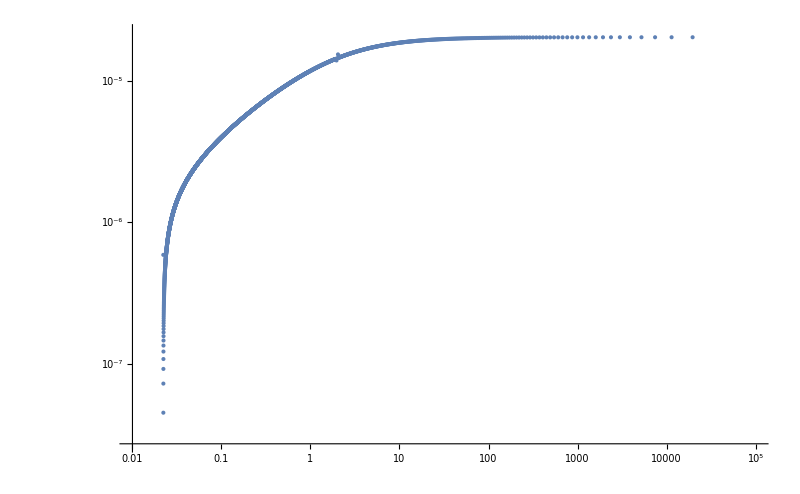

```mathematica
ListLogLogPlot[Abs[Re[listbeta]],PlotRange->{{1*10^-2,1*10^5},{0,2.2*10^-5}},ImageSize->800]
```

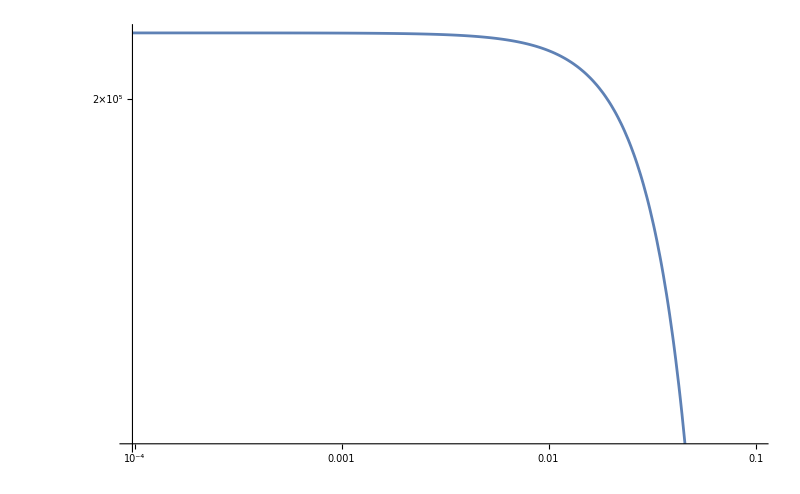

```mathematica
LogLogPlot[-Im[gammaincomp[ρ1,ρ2,U1,U2,kx,g,B]],{B,0,0.1},ImageSize->800]
```

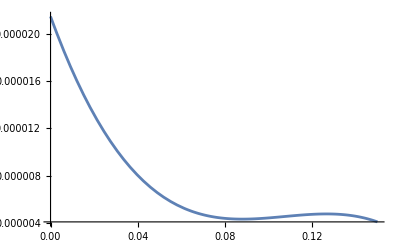

```mathematica
Plot[-0.01519*x^3+0.00489*x^2-0.0005077*x+2.148*10^(-5),{x,0,0.15}]
```

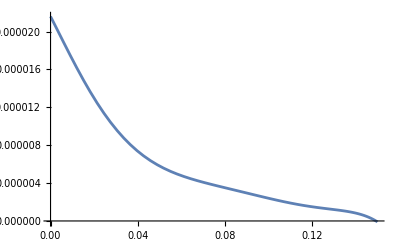

```mathematica
Plot[1.488*x^7-38.81*x^6+17.6*x^5-2.961*x^4+0.2068*x^3-0.002234*x^2-0.000449*x+2.16*10^(-5),{x,0,0.15}]
```

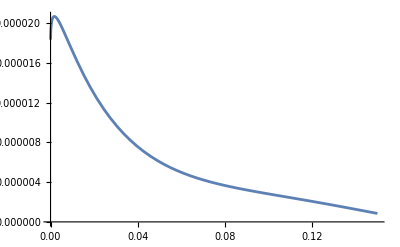

```mathematica
Plot[0.001613*x^(3/4)-0.00916x+0.01217x^3-0.01217x^2+0.01286x^(5/4)+1.834*10^(-5),{x,0,0.15}]
```

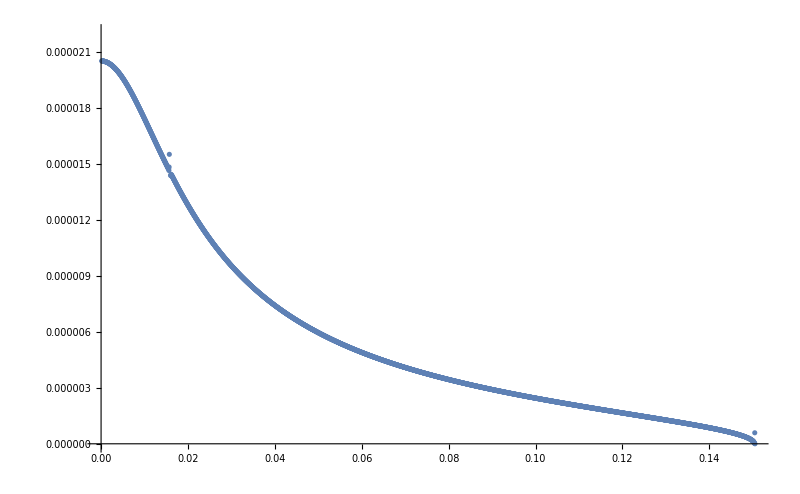

```mathematica
ListPlot[Abs[Re[list]],PlotRange->{{0,0.1505},{0,2.2*10^-5}},ImageSize->800]
```

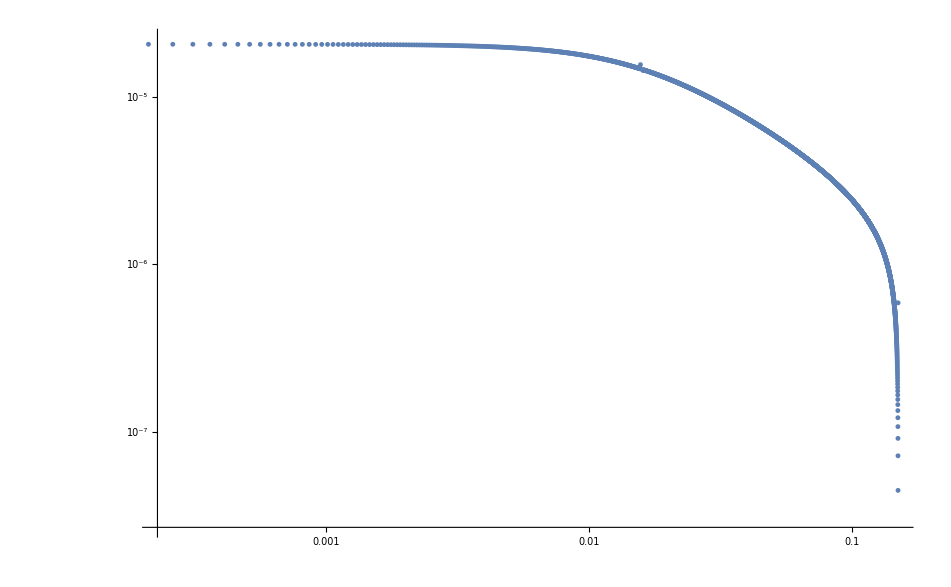

```mathematica
ListLogLogPlot[Abs[Re[list]],PlotRange->{{0,0.1505},{0,2.2*10^-5}}]
```

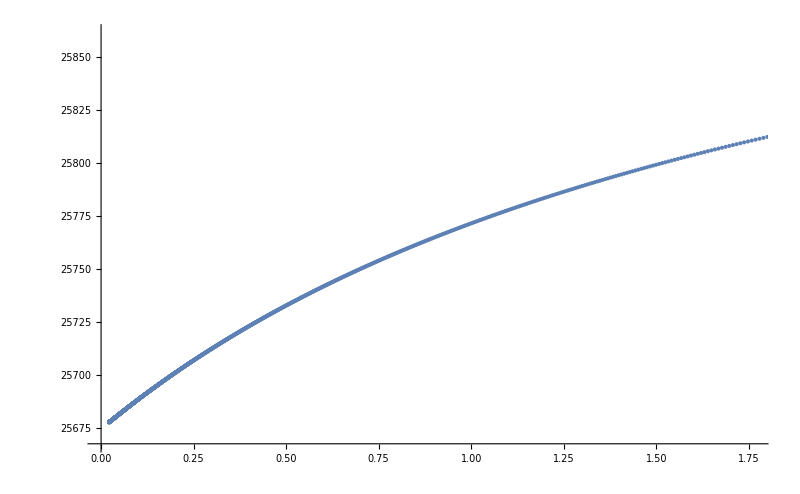

```mathematica
ListPlot[Abs[listbeta],ImageSize->800]
```